{{a[1]→0.002,b[1]→0.0691147}}

{{a[2]→0.764464,b[2]→-0.00713171}}

{{a[3]→0.061604,b[3]→-0.000103107}}

{a[4]→0.0100503,b[4]→0}

Piecewise[{{0.002+0.0691147 t, 0≤t≤10}, {0.764464-0.00713171 t, 10≤t≤100}, {0.061604-0.000103107 t, 100≤t≤500}, {0.0100503, True}}]

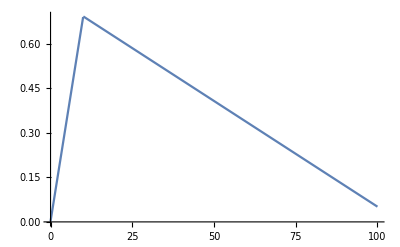

```mathematica
(* Different approach: suppose δ is piecewise affine continuous *)
time = {0,10, 100,500};

(* Transition probabilities starting with p[0] = 1 *)
sTrans = {1,0.50,0.95,0.99};
δInit := 0.0020;

(* Compute delta coefficients *)
For[i=1, i<= Length[time]-1,i++, δ[i]=a[i]+b[i]*t  ];δ[Length[time]] = - Log[sTrans[[Length[time]]]];
sol[Length[time]] = {a[Length[time]] ->-Log[sTrans[[Length[time]]]],b[Length[time]] -> 0};

(* Compute coefficients *)
For[i=2, i<= Length[time]-1, i++, sol[i]= NSolve[{a[i]+b[i]* time[[i+1]] == -Log[sTrans[[i+1]]],a[i]+b[i]*time[[i]]== -Log[sTrans[[i]]] },{a[i],b[i]}]];
sol[1]=Solve[a[1]+b[1]* time[[2]]==-Log[sTrans[[2]]]&& a[1]+b[1]* time[[1]]== δInit, {a[1], b[1]}];
For[i=1, i<= Length[time], i++,Print[sol[i]]]

(* Replace coefficients in delta *)
For[i=1, i<= Length[time],i++, δ[i]=a[i]+b[i]*t/.sol[i]];

(* Define piecewise affine graph *)
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];

(* Return delta, unclear why this does not return deltaX *)
 δPiece= Piecewise[δGraph, δ[Length[time]]]

Plot[δPiece,{t,0,100}]
```

```mathematica
(* Define hamiltionian (simplified) *)
pDot = -δ*p;
mDot = r*m - x ;
sDot = g*s+b*x^β;
ϕ = q*B*(δ/δInit)^μ*DiracComb[t/10];
H = p*s^α*δ+vm*mDot+vp*pDot+vs*sDot
```

vm (m r-x)+vs (g s+b x^β)+p s^α δ-p vp δ

```mathematica
(* Differentiate H *)
dx = D[H,x];
dp = D[H,p];
dm = D[H,m];
ds = D[H,s] ;

(* Compute optimal values *)
(* Problem: need to solve numerically !*)
xStar = SolveValues[dx==0,x]
vmDot = -dp;
vmStar = DSolveValue[vm'[t]==(vmDot/.(vm->vm[t])),vm[t],t ]
vsDot = -ds;
vsStar = DSolveValue[vs'[t] == (vsDot/.(vs->vs[t])),vs[t],t]
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

{(vm/(b vs β))^(1/(-1+β))}

-s^α t δ+t vp δ+C[1]

-(p s^(-1+α) α δ)/g+ⅇ^(-g t) C[1]

```mathematica
vmDot
```

-s^α δ+vp δ

```mathematica
(* Solve s and m *)
sStar = DSolveValue[{s'[t]== (sDot/.vm ->vmStar/.vs->vsStar/.x->xStar/.s->s[t]),s[0]==0},s[t],t]
```

(b (-1+ⅇ^(g t)) x^β)/g

```mathematica
(* Define parameters *)
```